# parton.note.1.nb

```mathematica
NotebookFileName[]
```

D:\gitstorage\note\parton-df\parton.note.1.nb

## notation

k^+→k`p, k^-→k`m,k_⊥=k`perp,

Ω_ϕ→Ω`ϕ

baryon→ba

mesons→ϕ

## definition

d`ϕ[k_]:=k^2-(m`ϕ)^2+I ϵ==k`p*k`m-k`perp-(m`ϕ)^2+I ϵ==k`p*k`m-Ω`ϕ+I ϵ

d`ba[k_]:=(p-k)^2-(m`ba)^2+I ϵ==(p-k)`p*(p-k)`m-k`perp-(m`ba)^2+I ϵ==(p-k)`p*(p-k)`m-(Ω`ba)^2+I ϵ

Ω`ϕ:=(k`perp)^2+(m`ϕ)^2≥0

Ω`ba:=(k`perp)^2+(m`ba)^2≥0

k`p*k`m-(k`perp)^2=(m`ϕ)^2

p`p*p`m-(p`perp=0)^2=(m`ba)^2

## calc`1

```mathematica
mass`rule={
Ω`ϕ->(k`perp)^2+(m`ϕ)^2,Ω`ba->(k`perp)^2+(m`ba)^2,
k`p->y*p`p,p`m->(m`ba)^2/p`p
};
```

```mathematica
(
(
(p`p-k`p)*k`p*((p`m-(Ω`ϕ)/(k`p))-(Ω`ba)/(p`p-k`p))
)//.mass`rule
)//Simplify
```

-p`p ((k`perp)^2+(m`ba)^2 y^2-(-1+y) (m`ϕ)^2)

## calc`2

(∫^∞)_(-∞)ⅆk`m 1/(D`ϕ)==(∫^∞)_(-∞)ⅆk`m 1/(k`p*k`m-Ω`ϕ+I ϵ)

Simplify notation a little

((∫ⅆz)^∞)_(-∞)1/(z-a+I ϵ),a≥0

## if k`p > 0

单极点在 1/(k`p)(Ω_ϕ-I ϵ),(第四象限), 做一个顺时针的闭合回路，积分共有两部分，利用留数定理。

ParametricPlot[{{Cos[t],Sin[t]},{(2(t-3π/2))/π,0}},{t,π,2π}]

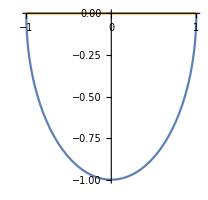

int+(∫_0)^-π(I R e^(I φ) ⅆφ)/(R e^(I φ)-a+I ϵ)+→

int+(∫_0)^(-π/2)(I R e^(I φ) ⅆφ)/(R e^(I φ)-a)=-2π I *(1)

```mathematica
int`b=Assuming[{R>a>ϵ>0},
Simplify[Integrate[I R Exp[I φ]/(R Exp[I φ]-a+I ϵ),{φ,0,-π}]]
]
```

-ⅈ π+2 ArcTanh[(a-ⅈ ϵ)/R]

## add and simplify

```mathematica
int`b`simlif=Assuming[{R>a>0},
Limit[int`b,ϵ->0,Direction->"FromAbove"]
]//Simplify
```

-ⅈ π+2 ArcTanh[a/R]

```mathematica
int`result=Assuming[{R>a>0},
(-2π I-int`b`simlif)/.{a->li*R}//Simplify
]
```

-ⅈ π-2 ArcTanh[li]

so,

int`result→-ⅈ π-2 ArcTanh[li]→(R→+∞,a/R→0)→-ⅈ π

## apply

∫ⅆk`m 1/(D`ϕ)==∫ⅆk`m 1/(k`p*k`m-Ω`ϕ+I ϵ),

∫ⅆz/(z-a+I ϵ)==-ⅈ π,a≥0

******************************************

∫ⅆk`m 1/(k`p*k`m-Ω`ϕ+I ϵ)→

if y≠0, then

→1/(k`p)∫ⅆ(k`p*k`m)1/(k`p*k`m-Ω`ϕ+I ϵ)→1/(k`p)∫ⅆz 1/(z-Ω`ϕ+I ϵ)→

1/(k`p)(-ⅈ π)→(-ⅈ π)1/y 1/(p`p)

## if k`p = 0

(∫^∞)_(-∞)ⅆk`m 1/(k`p*k`m-Ω`ϕ+I ϵ)→1/(-Ω`ϕ+I ϵ)(∫^∞)_(-∞)ⅆk`m→∞ (k`p=0)

## if k`p < 0

单极点在 1/(k`p)(Ω_ϕ-I ϵ)(第二象限), 做一个顺时针的闭合回路，积分共有两部分，利用留数定理。

积分回路中不包含极点，所以和为0

ParametricPlot[{{Cos[t],Sin[t]},{(2(t-3π/2))/π,0}},{t,π,2π}]

-Graphics-

int+(∫_0)^-π(I R e^(I φ) ⅆφ)/(R e^(I φ)-a+I ϵ)+→

int+(∫_0)^(-π/2)(I R e^(I φ) ⅆφ)/(R e^(I φ)-a)=0

so,

1/(k`p)∫ⅆ(k`p*k`m)1/(k`p*k`m-Ω`ϕ+I ϵ)==-1/(k`p)(∫_0)^-π arc==-1/(k`p)(-ⅈ π)==1/(k`p)ⅈ π

**************************************************

conclusion

1/(k`p)∫ⅆ(k`p*k`m)1/(k`p*k`m-Ω`ϕ+I ϵ)

k`p*k`m-Ω`ϕ+I ϵ, can be written as,

k`p*(k`m-(Ω`ϕ-I ϵ)/(k`p)),

********************

k`p>0,

(k`p+I δ Ω`ϕ)(k`m-((Ω`ϕ)/(k`p)-I k`p δ))→第四象限

k`p k`m -Ω`ϕ+ⅈ δ((k`p)^2 +  (Ω`ϕ)/(k`p)(k`p k`m- Ω`ϕ))

k`p k`m- Ω`ϕ==k^2-(m`ϕ)^2+I ϵ≥0, 在积分之后,写成费曼截面的时候,总是正的--on shell

so,ⅈ δ((k`p)^2 +  (Ω`ϕ)/(k`p)(k`p k`m- Ω`ϕ))always positive, can be noted as ⅈ ϵ,

k`p k`m -Ω`ϕ+ⅈ δ((k`p)^2 +  (Ω`ϕ)/(k`p)(k`p k`m- Ω`ϕ))→k`p k`m -Ω`ϕ+ⅈ ϵ

**************************************

k`p<0,

(k`p-I δ Ω`ϕ)(k`m-((Ω`ϕ)/(k`p)-I k`p δ))→第二象限

k`m k`p-Ω`ϕ+ⅈ δ((k`p)^2 - (Ω`ϕ)/(k`p)(k`p k`m  - Ω`ϕ))

ⅈ δ((k`p)^2 - (Ω`ϕ)/(k`p)(k`p k`m  - Ω`ϕ)) always positive ,can be noted as ⅈ ϵ,

k`p k`m -Ω`ϕ+ⅈ δ((k`p)^2 - (Ω`ϕ)/(k`p)(k`p k`m  - Ω`ϕ))→k`p k`m -Ω`ϕ+ⅈ ϵ

****************************************

1/(k`p)∫ⅆ(k`p*k`m)1/(k`p*k`m-Ω`ϕ+I ϵ)→ (-ⅈ π θ[k`p])/(k`p+I δ Ω`ϕ)+(ⅈ π θ[-k`p])/(k`p-I δ Ω`ϕ),δ→0

其中θ[k`p]是阶跃函数

*********************

## another side

Few - Body Syst (2012) 52 : 421–426,light - front dynamics (LFD)

a simple example of two - dimensional loop amplitude for a particle of mass m :

ii=∫ⅆ^2 k 1/(k^2-m^2+I ϵ)

In the covariant approach, this amplitude can be computed by dimensional regulation and is given by

ii=-I π(2/(2-d)-Log[π]-γ+O[2-d]-Log[m^2/μ^2])

where μ is a mass parameter introduced to give the correct mass dimensions in d dimensions, 
γ ≈ 0.577 is  Euler' s constant, 
and d goes to 2 in this example

The LNA behavior of this amplitude in the limit m→0 is thus given by I[LNA]=I π log[m^2].

In time - ordered perturbation theory, it is straightforward to use Cauchy' s integral theorem and compute the amplitude as follows :

ii=∫ⅆ k^1ⅆ k^0 1/((k^0+ω_k-I ϵ)(k^0-ω_k+I ϵ))→Lower halp plane

-2π I∫_(-∞)^(Λ→ ∞) ⅆ k^1*1/(2 √((k^1)^2+m^2))→-2π I∫_0^(Λ→ ∞) ⅆ k^1*1/(√((k^1)^2+m^2))→

(-2π I)(-1/2 Log[1-k/(√(k^2+m^2))]+1/2 Log[1+k/(√(k^2+m^2))])@{0,Λ→+∞}→

(-2π I)(-1/2Log[m^2/(2 Λ^2)]+1/2 Log[2] )→ (2π I)(1/2 Log[m^2/(2 Λ^2)]-1/2 Log[2] )

lim_(Λ→∞)  2π I Log[m/(2Λ)]

in which, ω_k=√((k^1)^2+m^2)

The LNA behavior of this amplitude is identical to ILNA=I π Log[m^2].

However, the LFD calculation of this amplitude is not so simple due to a dramatic change of pole structure

A0=∫ⅆ^2 k 1/(k^2-m^2+I ϵ)

A0=1/2*∫_(-∞)^∞ ⅆk`p∫_(-∞)^∞ ⅆk`m 1/(k`p k`m-m^2+I ϵ)→

=1/2*∫_(-∞)^∞ ⅆk`p∫_(-∞)^∞ ⅆu/u 1/(k`p -(m^2-I ϵ)u)

=1/2*∫_(-∞)^∞ ⅆk`p∫_(-∞)^∞ ⅆu*1/2(1/(u+I δ)+1/(u-I δ))1/(k`p -(m^2-I ϵ)u)→

in which, u=1/(k`m),

*******************************************************

and in the last line split the 1/u denominator  into two poles off the real u axis.

This split produces just the correct result, as we shall see. 
Before applying this form to our integrals, we make a final step for the tadpole.

After the k`m integration has been carried out, which can be done safely using the residue theorem as the integral over u is convergent,

a divergent k`p integral appears that must be regulated.

We do that by using a finite cutoff. The result is,

*******************************************************

cauchy theorem→

if k`p>0, singularity{0,-I δ,Iδ,(k`p)/(m^2-I ϵ)(first quadrant)}

if k`p<0, singularity{0,-I δ,Iδ,(k`p)/(m^2-I ϵ)(third quadrant)}

*****************************************

if k`p>0,

1/2*∫_(-∞)^∞ ⅆk`p(-2π I)*1/2 1/(k`p -(m^2-I ϵ)(-I δ))θ(k`p)
if k`p<0,

1/2*∫_(-∞)^∞ ⅆk`p(+2π I)*1/2 1/(k`p -(m^2-I ϵ)(I δ))θ(-k`p)

*********************************

A0=1/2*∫_(-∞)^∞ (ⅆk`p(-I π )(θ(k`p))/(k`p +I δ m^2)+(+I π )(θ(-k`p))/(k`p -I δ m^2))→

∫_0^∞ ⅆk`p(-I π)/(k`p +I δ m^2)→lim_(Λ→+∞) ∫_0^Λ ⅆk`p(-I π)/(k`p +I δ m^2)→

lim_(Λ→+∞) (-I π )Log[k`p+I δ m^2]@{Λ,0}→

(-I π )(Log[Λ+I δ m^2]-Log[I δ m^2])==(-I π )(Log[Λ/I δ]-Log[m^2])

This may be compared to the result from dimensional regularization

A0=-I π(1/ϵ-γ+Log[4π]-Log[m^2/μ^2])+O[ϵ]

Clearly, the correct dependence on the mass of the covariant amplitude is reproduced by the LF calculation

```mathematica
int`dr=Integrate[r/(r^2 Sin[ϕ]Cos[ϕ]-m^2+I ϵ),r,Assumptions->{r>0,m>0 ,ϵ>0}]
```

1/2 Csc[ϕ] Log[-m^2+ⅈ ϵ+r^2 Cos[ϕ] Sin[ϕ]] Sec[ϕ]

```mathematica
int`dr`limit=Assuming[{R>m>0 ,ϵ>0},
Simplify[(int`dr/.r->R)-(int`dr/.r->0)/.ϵ->0]
]
```

-1/2 Csc[ϕ] (Log[-m^2]-Log[-m^2+R^2 Cos[ϕ] Sin[ϕ]]) Sec[ϕ]

```mathematica
int`dr`dϕ=Integrate[int`dr`limit,{ϕ,0,2π},Assumptions->{R>m>0 }]
```

$Aborted

```mathematica
Integrate[-1/(2x)Log[-m^2/(-m^2+R^2 x)],{ϕ,0,2π},Assumptions->{R>m>0 }]
```

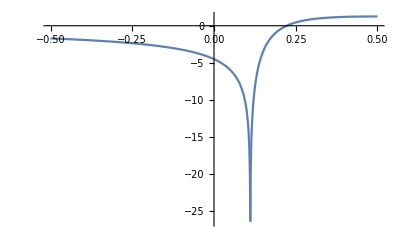

```mathematica
Block[{m=1,R=3},
Plot[
Piecewise[{
{-1/(2x)Log[-m^2/(-m^2+R^2 x)],x<0},
{-1/2,x==0},
{-1/(2x)Log[-m^2/(-m^2+R^2 x)],0<x<m^2/R^2},
{R^(2□),x==m^2/R^2},
{-1/(2x)Log[m^2/(-m^2+R^2 x)],x>m^2/R^2}
}
]
,{x,-1/2,1/2}
,PlotRange->All
]
]
```